# The Relative Entropy of Coherence quantifies Performance in Bayesian Metrology

Ruvi Lecamwasam, January 2024
me@ruvi.blog

Code for the Example in article ‘The Relative Entropy of Coherence quantifies Performance in Bayesian Metrology’

## Base functions

```mathematica
σx=({{0, 1}, {1, 0}});σy=({{0, -ⅈ}, {ⅈ, 0}});σz=({{1, 0}, {0, -1}});id=({{1, 0}, {0, 1}});

(* A density matrix on the Bloch sphere making angle θ with the Subscript[σ, z]-up state, and ϕ with the Subscript[σ, x]-up state in the Subscript[σ, x] Subscript[σ, y]-plane *)
ρupθϕ[θ_,ϕ_]:=With[
{
x=Sin[θ]Cos[ϕ],
y=Sin[θ]Sin[ϕ],
z=Cos[θ]
},
1/2(id+x σx+y σy+z σz)
]
(* The density matrix orthogonal to ρupθϕ *)
ρdownθϕ[θ_,ϕ_]:=With[
{
x=Sin[θ]Cos[ϕ],
y=Sin[θ]Sin[ϕ],
z=Cos[θ]
},
1/2(id-x σx-y σy-z σz)
]

(* Same as above just expressed as states *)
ψupθϕ[θ_,ϕ_]:={Cos[θ/2],ⅇ^(ⅈ ϕ)Sin[θ/2]};
ψdownθϕ[θ_,ϕ_]:={Cos[(π+θ)/2],ⅇ^(ⅈ ϕ)Sin[(π+θ)/2]};
```

```mathematica
(* Von Neumann entropy *)
Options[S]={simplify->True};
S[ρ_,OptionsPattern[]] := Module[{evals},
	evals=Chop@Eigenvalues[ρ];
	
	If[OptionValue@simplify,evals=FullSimplify@evals];
	
	evals = DeleteCases[evals,0];

	(* Old, can't handle symbolic matrices
(* Select non-zero eigenvalues, this will be empty for a pure state *)
	evals = Select[Chop@Eigenvalues[ρ],#>0&];
	(* Return zero entropy for a pure state *)
*)
	If[Length@evals>0,
		-# Log[#]&/@evals//Total,
	0]
]

(* Remove all off-diagonal elements of a density matrix *)
Δ[ρ_] := DiagonalMatrix@Diagonal@ρ;

(* Represent a density matrix ρ in the basis of states corresponding to θϕ *)
toθϕBasis[σ_,θ_,ϕ_]:=Module[
{
ψup=ψupθϕ[θ,ϕ],
ψdown=ψdownθϕ[θ,ϕ],

θϕBasis
},

θϕBasis={ψup,ψdown};

Table[ConjugateTranspose[ψj].σ.ψk,{ψj,θϕBasis},{ψk,θϕBasis}]
]

(* Find the relative entropy of coherence of a state ρ, in the basis of states corresponding to θϕ *)
Cθϕ[ρ_,θ_,ϕ_]:=Module[
{ρθϕ},

ρθϕ=toθϕBasis[ρ,θ,ϕ];

S@Δ@ρθϕ-S@ρθϕ
]
(* Find the ensemble coherence of an ensemble consisting of Subscript[ρ, 1],Subscript[ρ, 2] with equal probability, in the basis of states corresponding to θϕ *)
Ceθϕ[ρ1_,ρ2_,θ_,ϕ_]:=Module[
{Ci,
Cf},

Ci=1/2 Cθϕ[ρ1,θ,ϕ]+1/2 Cθϕ[ρ2,θ,ϕ];

Cf=Cθϕ[1/2(ρ1+ρ2),θ,ϕ];

Ci-Cf
]

(* Holevo information between two states *)
χ[ρ1_,ρ2_]:=S[1/2(ρ1+ρ2)]-(1/2 S[ρ1]+1/2 S[ρ2]);
```

## Figure 1: Coherence on the Bloch sphere

### Functions

```mathematica
(* Find the coherence between two states as a function of θ and ϕ *)
Options[Coherenceθϕ]={Δθ->π/15.,Δϕ->(2π)/30.,interpolate->True,parallel->True,normaliseByχ->True};
Coherenceθϕ[ρ1_,ρ2_,OptionsPattern[]]:=Module[
{table,CeData,χ},
table=If[OptionValue@parallel,ParallelTable,Table];

If[OptionValue@normaliseByχ,
χ=S[1/2(ρ1+ρ2)]-(1/2 S[ρ1]+1/2 S[ρ2]),
χ=1];

CeData=table[{θ,ϕ,1/χ Ceθϕ[ρ1,ρ2,θ,ϕ]},{θ,0,π,OptionValue@Δθ},{ϕ,0,2π,OptionValue@Δϕ}]//Flatten[#,1]&;

If[OptionValue@interpolate,Interpolation@CeData,CeData]

]
```

### Holevo informations

```mathematica
(* Holevo informations of states used in the example *)
χ[ρupθϕ[π/2,0],ρupθϕ[π/2,π/10.]]
χ[ρupθϕ[π/2,0],ρupθϕ[π/2,π/2.]]
χ[ρupθϕ[π/2,0],ρupθϕ[π/2.,π]]
```

0.0374722

0.416496

0.693147

### Spherical plots

```mathematica
θval=π;
ρ0=ρupθϕ[π/2,0];
cfunπ10=Coherenceθϕ[ρ0,ρθ=ρupθϕ[π/2,π/10]];
cfunπ2=Coherenceθϕ[ρ0,ρθ=ρupθϕ[π/2,π/2]];
cfunπ=Coherenceθϕ[ρ0,ρθ=ρupθϕ[π/2,π]];
```

```mathematica
colorScheme="DarkRainbow";

PlotSphereCoherence[cfun_,label_]:=SphericalPlot3D[1,{θ,0,π},{ϕ,0,2 π},

ColorFunction->Function[{x,y,z,θ,ϕ,r},ColorData[colorScheme][cfun[θ,ϕ]]],ColorFunctionScaling->False
,AxesLabel->{x,y,z}
,PlotLabel->label
,LabelStyle->Directive[FontColor->Black,FontSize->20]
,ImageSize->Medium,PlotRangePadding->0.1];

legend=BarLegend[colorScheme,LegendLayout->"Row"]

PlotSphereCoherence[cfunπ10,"π/10"]
PlotSphereCoherence[cfunπ2,"π/2"]
PlotSphereCoherence[cfunπ,"π"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### Exporting data

To make the nice Bloch sphere plots in Figure 1a, I exported the coherence plots and rendered them in Blender. This function generates a so-called ‘uv’ map that can then be used to texture a sphere.

```mathematica
MakeUV[θ_]:=Module[
{
colorFunction
},

colorFunction=Coherenceθϕ[ρ0,ρθ=ρupθϕ[π/2.,θ]];

RegionPlot[True,{ϕ,0,2π},{θm,0,π},ColorFunction->Function[{ϕ,θm},ColorData[colorScheme][colorFunction[π-θm,ϕ]]],ColorFunctionScaling->False
,LabelStyle->Directive[FontSize->20,FontColor->Black]
,Frame->True,GridLines->{Table[0,2π,2π/10],None},FrameLabel->{"ϕ", "π-θ"},PlotPoints->100,MaxRecursion->6,ImageSize->Large]
]
```

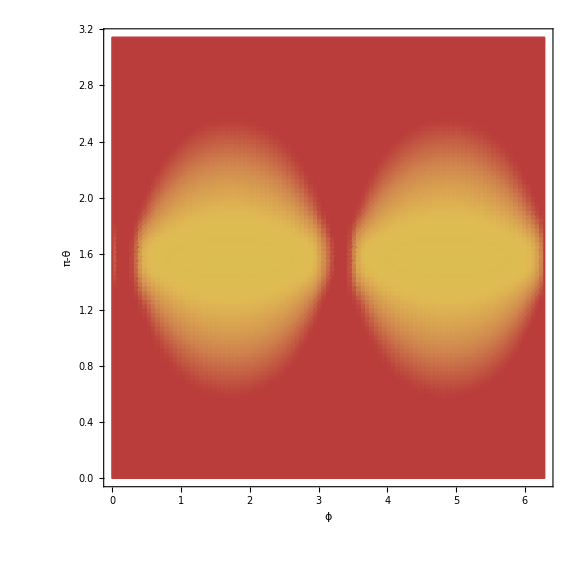

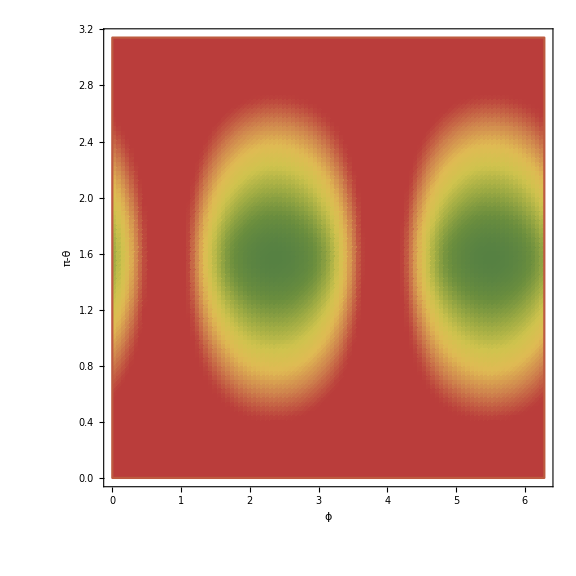

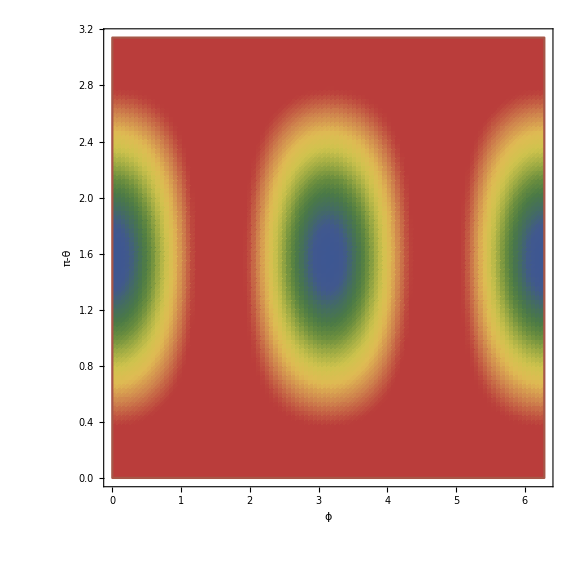

```mathematica
MakeUV[π/10]
MakeUV[π/2]
MakeUV[π]
```

## Figure 2a: Coherences

### Projective measurement

```mathematica
(* Find minimum enseble coherence for a projective measurement, to discriminate between ρ1,ρ2 *)
Options[FindMinCe]={normaliseByχ->True,analyticBestθϕ->None};
FindMinCe[ρ1_,ρ2_,OptionsPattern[]]:=Module[
{CeFunc,minCe,χVal},

If[OptionValue@analyticBestθϕ===None,

CeFunc=Coherenceθϕ[ρ1,ρ2,parallel->False,normaliseByχ->OptionValue@normaliseByχ];
minCe=First@NMinimize[{CeFunc[θ,ϕ],0<θ<ϕ,0<ϕ<2π},{θ,ϕ}]
,

If[OptionValue@normaliseByχ,
χVal=S[1/2(ρ1+ρ2)]-(1/2 S[ρ1]+1/2 S[ρ2]),
χVal=1];

minCe=1/χVal Ceθϕ[ρ1,ρ2,π/2,OptionValue@analyticBestθϕ];
];

minCe
]
```

```mathematica
θList={1.0*π,π/2.,π/10.};
ceProjectiveList=Table[With[{θ=theta},FindMinCe[ρupθϕ[π/2,0],ρupθϕ[π/2,θ],analyticBestθϕ->(θ/2+π/2)]],{theta,θList}]
```

{0.,0.335763,0.672123}

### Unambiguous state discrimination

```mathematica
(* Decohere in the basis Π *)
ΔV[ρ_,ΠList_]:=Sum[ΠList[[j]].ρ.ΠList[[j]],{j,1,Length@ΠList}]

(* Coherence in the basis Π *)
CV[ρ_,ΠList_]:=S@ΔV[ρ,ΠList]-S@ρ

(* Ensemble coherence in the basis Π *)
CeV[ρ1_,ρ2_,ΠList_]:=Module[
{Ci,
Cf},

Ci=1/2 CV[ρ1,ΠList]+1/2 CV[ρ2,ΠList];

Cf=CV[1/2(ρ1+ρ2),ΠList];

Ci-Cf
];
```

```mathematica
(* Find ensemble coherence when the states are separated by an angle θ *)
FindPOVMCe[θ_]:=Module[
{ρ1,ρ2
,χVal
,Π1,Π2,c,E1,E2,E0
,M1,M2,M0,MList
,jList,j2List
,V,Vt,ρV1,ρV2
,MVList,ΠList
,ceΠ,ceM},

(* Construct the two states *)
ρ1=ρupθϕ[π/2.,0.];
ρ2=ρupθϕ[π/2.,θ];

(* Find the Holevo information *)
χVal=χ[ρ1,ρ2];

(* Construct the POVM measurement operators *)
Π1=id-ρ2;
Π2=id-ρ1;
c=Max@Eigenvalues[Π1+Π2];

E1=Π1/c;
E2=Π2/c;
E0=id-E1-E2;

(* Take the square roots of the operators *)
M1=MatrixPower[E1,0.5]//Chop;
M2=MatrixPower[E2,0.5]//Chop;
M0=MatrixPower[E0,0.5]//Chop;

MList={M0,M1,M2};
jList={({{1}, {0}, {0}}),({{0}, {1}, {0}}),({{0}, {0}, {1}})};

(* Construct the dilation map *)
j2List=KroneckerProduct[#,Transpose@#]&/@jList;
V=Sum[KroneckerProduct[MList[[j]],jList[[j]]],{j,1,3}]//Chop;
Vt=ConjugateTranspose[V];

(* Dilate both states to the larger Hilbert space *)
ρV1=V.ρ1.Vt;
ρV2=V.ρ2.Vt;

(* Corresponding projective measurement *)
ΠList=Table[KroneckerProduct[id,j2List[[j]]],{j,1,3}];

1/χVal CeV[ρV1,ρV2,ΠList]
]
```

```mathematica
ϕList={1.0*π,π/2.,π/10.};
cePOVMList=Table[With[{ϕ=phi},FindPOVMCe[ϕ]],{phi,ϕList}]
```

{-1.60171×10^-16,0.512556,0.772263}

### Plot the coherences

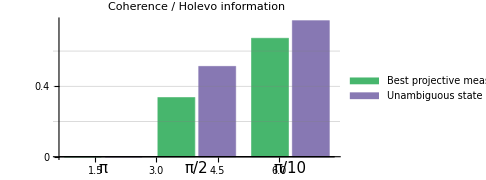

```mathematica
groupLabels={"π","π/2","π/10"};
barLabels={"",""};

data=Transpose@{ceProjectiveList,cePOVMList};

coherencePlot=BarChart[data,
ChartStyle->{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.528488, 0.470624, 0.701351]},
(*,ColorFunction->"DarkRainbow",ColorFunctionScaling->False,*)
ChartLabels->{Placed[groupLabels,Below],Placed[barLabels,Above]},ChartLegends->Placed[{"Best projective\nmeasurement","Unambiguous state\ndiscrimination"},{0.25,0.7}],
TicksStyle->Directive[FontSize->15],LabelStyle->Directive[FontSize->15],Ticks->{Automatic,Join[{0},Range[0.2,1,0.2]]}
,AspectRatio->0.5,
PlotRange->{All,{Automatic,1}},
PlotLabel->Style["Coherence / Holevo information",Directive[FontColor->Black]]
,ImageSize->Medium
,GridLines->{None,{0.2,0.4,0.6,0.8,1}}
]
```

## Figure 2b: Error probabilities

### Error probabilities

```mathematica
(* Find the error probabilities for projective measurement and unambiguous state discrimination when the states are separated by θ *)
ErrorProbabilities[θVal_]:=Module[
{ρ0,ρ1,Π0,Π1,id,Π0c,Π1c,c,E0,E1,En,
psProj,psPOVM,ρθ},

(* Construct the two states *)
ρθ[θ_]:=ρupθϕ[π/2,θ];

ρ0=ρθ[0];
ρ1=ρθ[θVal];

(* Optimal projective basis *)
Π0=ρθ[θVal/2-π/2];
Π1=ρθ[θVal/2+π/2];

(* Success probability for a projective measurement *)
psProj=1/2(Tr[Π0.ρ0+Π1.ρ1]);

(* Construct the POVM *)
id=IdentityMatrix[2];
Π0c=id-ρ0;
Π1c=id-ρ1;
c=Max@Eigenvalues[Π0c+Π1c];
E0=Π0c/c;
E1=Π1c/c;
En=id-E0-E1;

(* Success proability for the POVM *)
psPOVM=1/2(Tr[(E1+En/2).ρ0+(E0+En/2).ρ1]);

(* Return the error probabilities *)
{1-psProj,1-psPOVM}//N//Chop
]

ϕList={π,π/2,π/10};
data=ErrorProbabilities/@ϕList
```

{{0,0},{0.146447,0.353553},{0.421783,0.493844}}

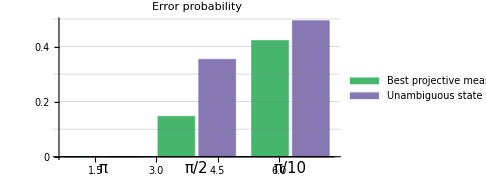

```mathematica
groupLabels={"π","π/2","π/10"};
barLabels={"",""};
errorPlot=BarChart[data,
ChartStyle->{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.528488, 0.470624, 0.701351]},
(*,ColorFunction->"DarkRainbow",ColorFunctionScaling->False,*)
ChartLabels->{Placed[groupLabels,Below],Placed[barLabels,Above]},ChartLegends->Placed[{"Best projective\nmeasurement","Unambiguous state\ndiscrimination"},{0.25,0.7}],
TicksStyle->Directive[FontSize->15],LabelStyle->Directive[FontSize->15],Ticks->{Automatic,Join[{0},Range[0.1,0.5,0.1]]}
,AspectRatio->0.5,PlotRange->{All,{Automatic,Automatic}},PlotLabel->Style["Error probability",Directive[FontColor->Black]]
,ImageSize->Medium
,GridLines->{None,{0.1,0.2,0.3,0.4,0.5}}
]
```